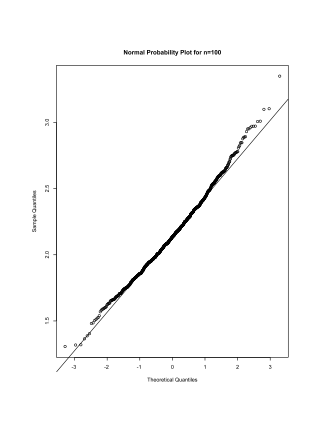
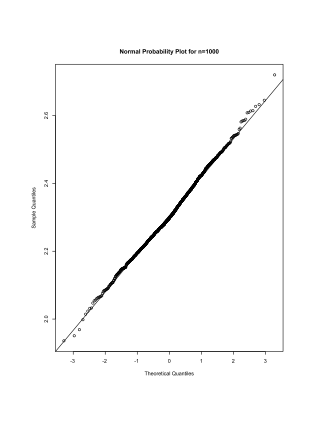
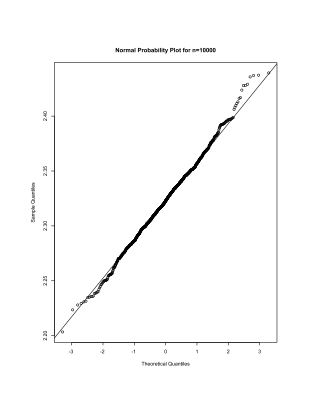
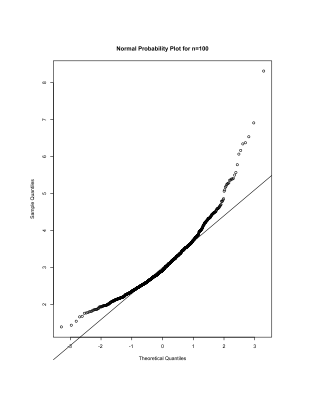
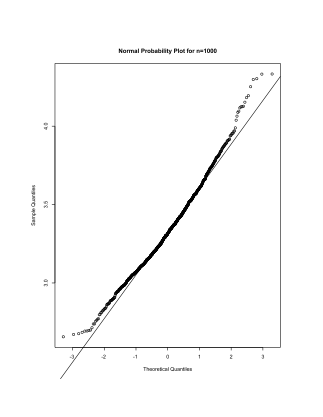
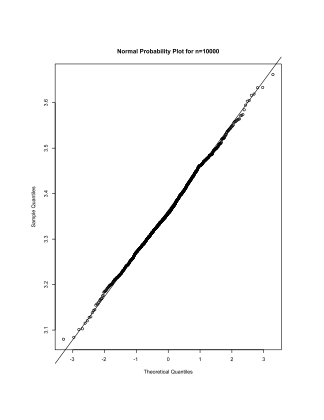
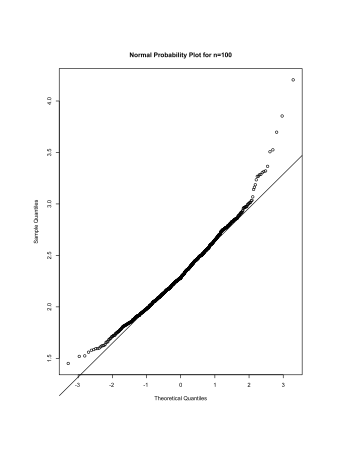
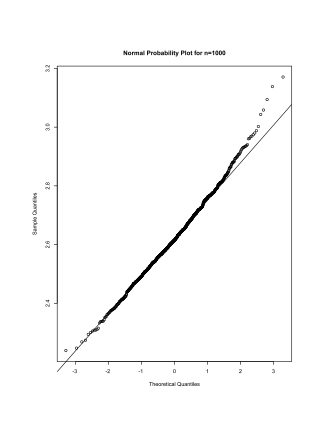
Zixian Francis Lin
Professor Lehoczky
Risk Management 1 Homework 1
9/6/2017

Problem 1: Practice on VaR versus Shortfall VaR

Parameters: 

α_1=0.90
α_2=0.95
α_3=0.975
α_4=0.99
α_5=0.995

a)

Underlying security with notional n=$10,000.

Case 1: The daily log returns (-losses) are normally distributed.

μ=0 

σ=0.2/(√250)


μ'=nμ

σ'=n 0.2/(√250)


Formulas for VaR and expected shortfall S_α: 

VaR_α=μ'+σ'Φ^-1(α)
S_α=μ'+σ'/(1-α)ϕ(Φ^-1(α))

(1) α_1=0.90
VaR_α=$162.10
S_α=$221.99

(2) α_2=0.95
VaR_α=$208.06
S_α=$260.91

(3) α_3=0.975
VaR_α=$247.92
S_α=$295.71

(4) α_4=0.99
VaR_α=$294.26
S_α=$337.13

(5) α_5=0.995
VaR_α=$325.82
S_α=$365.81

Case 2: The daily log return (-losses) are t-4 distributed with v=4. Hence, we need to pick σ √(v/(v-2))=0.2/(√250).

σ=0.2/(√500)
μ=0 


μ'=nμ

σ'=n 0.2/(√500)

Formulas for VaR and expected shortfall S_α: 

VaR_α=μ'+σ'Τ^-1(α)
S_α=μ'+σ'(τ( Τ^-1(α)))/(1-α)((v+(Τ^-1(α))^2)/(v-1))

(1) α_1=0.90
VaR_α=$137.13
S_α=$223.55

(2) α_2=0.95
VaR_α=$190.68
S_α=$286.47

(3) α_3=0.975
VaR_α=$248.33
S_α=$357.19

(4) α_4=0.99
VaR_α=$335.14
S_α=$466.94

(5) α_5=0.995
VaR_α=$411.80
S_α=$565.71

Comment:
Between normal and t distributions for the losses, the t distribution has fatter tail than normal distribution does. Hence, To achieve the same alpha, the VaR (the alpha quantile) needs to be larger at the tail end. 
Expected shortfalls are also larger for t distribution case than the case of normal distribution for the same level of alpha. Since the tail for t distribution is fatter, it will make the expected value of loss beyond VaR quantile larger than the expected value of loss beyond VaR quantile in the normal distribution case. There is more probability that very extreme value in the tail happens for fatter tail distribution. 

b) 

10 underlying stocks with n’=$1,000 notional position each.


Case 1: The daily log returns (-losses) are normally distributed.

For each stock, the notional n’ is $1,000. 

μ=0 

σ=0.2/(√250)


μ'=n'μ

σ'=n' 0.2/(√250)

Since sum of 10 same indeprendent normally distributed random variables also have normal distribution with


μ''=10*μ'=0

σ''=√10*σ'=√10*n' 0.2/(√250)


Formulas for VaR and expected shortfall S_α: 

VaR_α=μ''+σ''Φ^-1(α)
S_α=μ''+σ''/(1-α)ϕ(Φ^-1(α))

Hence, we can use the formula to calculate VaR and expected shortfall in this case.

(1) α_1=0.90
VaR_α=$51.26
S_α=$70.20

(2) α_2=0.95
VaR_α=$65.79
S_α=$82.51

(3) α_3=0.975
VaR_α=$78.40
S_α=$93.51

(4) α_4=0.99
VaR_α=$93.05
S_α=$106.61

(5) α_5=0.995
VaR_α=$103.03
S_α=$115.68

Case 2: The daily log return (-losses) are t-4 distributed with v=4. Hence, we need to pick σ √(v/(v-2))=0.2/(√250).

σ=0.2/(√500)
μ=0 

For each stock, the notional n is $1,000 

μ'=nμ
σ'=n 0.2/(√500)

Since the sum of 10 t-distributed random variables doesn’t have a named distribution, we have to use Monte Carlo Simulation to calculate VaR and expected shortfall.

We will use N=10,000 trials to do Monte Carlo simulation.

The linearized loss function is L=-∑_(i=1)^10 (μ'Δ+σ' T_i).

Hence, we can use Monte Carlo Simulation to calculate VaR and expected shortfall in this case.

(1) α_1=0.90
VaR_α=$49.57
S_α=$72.33

(2) α_2=0.95
VaR_α=$64.92
S_α=$87.83

(3) α_3=0.975
VaR_α=$80.28
S_α=$103.98

(4) α_4=0.99
VaR_α=$100.22
S_α=$126.89

(5) α_5=0.995
VaR_α=$122.14
S_α=$144.33

Comment:
In both cases (normally distirbuted and t-4 distributed log returns), VaR and expected shortfall of part(b) are both smaller than those in part (a) due to the diversification effect of holding more than one stock position for the same-value portfolio. 

c)

For 10 day 99% VaR, Δ=10. We will use N=10,000 trails Monte Carlo simulation to calculate VaR and expected shortfall. We are still working on a portfolio with 10 stocks in it with each stock’s position being $1.000. 

Case 1: The daily log returns (losses) are normally distributed. 

(Result) α_4=0.99
VaR_α=$294.51
S_α=$334.17
Case 2: The daily log return (-losses) are t-4 distributed with v=4. Hence, we need to pick σ √(v/(v-2))=0.2/(√250).

σ=0.2/(√500)
μ=0 

For each stock, the notional n is $1,000 

μ'=nμ
σ'=n 0.2/(√500)

Since the sum of 10 t-distributed random variables doesn’t have a named distribution, we have to use Monte Carlo Simulation to calculate VaR and expected shortfall.

We will use N=10,000 trials to do Monte Carlo simulation.

The linearized loss function is L=-∑_(i=1)^10 (μ'Δ+σ'∑_(j=1)^10 T_j).

(Result) α_4=0.99
VaR_α=$296.32
S_α=$340.83

Comment: In both cases, the result of 10-day 99% VaR is roughly √10times 1-day 99% VaR. 

R-code for Problem 1: 
# Problem 1 Practice on VaR versus Shortfall VaR
# Part (a) One stock with position $10,000
# Normal distributed returns
calcVarAndShortfallNormal<-function(mu, sig, alp)
{
  var=mu+sig*qnorm(alp)
  sf=mu+sig/(1-alp)*dnorm(qnorm(alp))
  return(cbind(alp,var,sf))
}
notional1=10000
mean=0
daily_sig=0.2/sqrt(250)
u=notional1*mean
sigma=notional1*daily_sig
alphas=c(0.90,0.95,0.975,0.99,0.995)
calcVarAndShortfall(u,sigma,alphas)
# t-4 distributed
calcVarAndShortfallT<-function(mu, sig, alp)
{
  var=mu+sig*qt(alp,df=4)
  sf=mu+sig*dt(qt(alp,df=4),df=4)/(1-alp)*(4+qt(alp,df=4)^2)/3
  return(cbind(alp,var,sf))
}
notional1=10000
mean=0
daily_sig=0.2/sqrt(500)
u=notional1*mean
sigma=notional1*daily_sig
calcVarAndShortfallT(u,sigma,alphas)
# Part (b)
# Normal distributed returns 
num_stock=10
notional2=1000
mean=0
daily_sig=0.2/sqrt(250)
u=num_stock*notional2*mean
sig=sqrt(num_stock)*notional2*daily_sig
calcVarAndShortfallNormal(u,sig,alphas)
# t-4 distributed
calcVarAndShortfallFromLossVector<-function(loss_vec, alp)
{
  loss_ordered=sort(loss_vec)
  n=length(loss_vec)
  var_pick=ceiling(n*alp)
  var=loss_ordered[var_pick]
  sf=mean(loss_ordered[var_pick:n])
  return(cbind(alp, var, sf))
}
N=10000
notional=1000
num_stock=10
mean=0
daily_sig=0.2/sqrt(500)
u=mean*notional
sig=daily_sig*notional
loss=numeric(N)
for (i in 1:N) 
{
  loss[i]=sum(u+sig*rt(num_stock,df=4))
}
for (i in 1:length(alphas))
{
  print(calcVarAndShortfallFromLossVector(loss, alphas[i]))
}
# Part (c)
# Normal distributed returns
delt=10
num_stock=10
notional2=1000
mean=0
daily_sig=0.2/sqrt(250)
u=mean*notional2
sig=daily_sig*notional2
N=10000    # Number of trails
loss=numeric(N)
for (i in 1:N)
{
  loss[i]=sum(u*delt+sig*sqrt(delt)*rnorm(10))
}
calcVarAndShortfallFromLossVector(loss,alphas[4])
# t-4 distributed
delt=10
N=10000
notional3=1000
num_stock=10
mean=0
daily_sig=0.2/sqrt(500)
u=mean*notional3
sig=daily_sig*notional3    # sigma for a single stock
loss=numeric(N)
for (i in 1:N)
{
  oneStockLoss=numeric(num_stock)
  for (j in 1:num_stock)
  {
    tFor10Days=sum(rt(10,df=4))
    oneStockLoss[j]=u*delt+sig*tFor10Days
  }
  loss[i]=sum(oneStockLoss)
}
calcVarAndShortfallFromLossVector(loss,alphas[4])

Problem 2: The asymptotic distribution of the sample quantile

a) 

N=1,000
α=0.99
F=N(0,1)

(1) n_1=100

Mean: 2.1503
Standard deviation: 0.2958
Theoretical mean: 2.3263
Theoretical standard deviation: 0.3733

-Graphics-

(2) n_2=1000

Mean: 2.3056
Standard deviation: 0.1141
Theoretical mean: 2.3263
Theoretical standard deviation:0.1181
-Graphics-
(3) n_3=10000

Mean: 2.3229
Standard deviation: 0.0365
Theoretical mean: 2.3263
Theoretical standard deviation: 0.0373

-Graphics-

b) 

N=1,000
α=0.99
F=t-distribution with df=5

(1) n_1=100

Mean: 3.0629
Standard deviation: 0.7776 
Theoretical mean: 3.3649
Theoretical standard deviation: 0.9119
-Graphics-
(2) n_2=1000

Mean: 3.3372
Standard deviation: 0.2784
Theoretical mean: 3.3649
Theoretical standard deviation: 0.2884

-Graphics-

(3) n_3=10000

Mean: 3.3617
Standard deviation: 0.0930
Theoretical mean: 3.3649
Theoretical standard deviation: 0.0912


-Graphics-

c) Normal plots of empirical shortfalls

N=1,000
α=0.99
F=N(0,1)

(1) n_1=100
Mean: 2.3166
Standard deviation: 0.3406 
-Graphics-

(2) n_2=1000
Mean: 2.6233
Standard deviation: 0.1354 
-Graphics-

(3) n_3=10000
Mean: 2.6611
Standard deviation: 0.0464
-Graphics-

N=1,000
α=0.99
F=t-distribution with df=5

(1) n_1=100
Mean: 3.5326
Standard deviation: 1.0017 
-Graphics-

(2) n_2=1000
Mean: 4.3173
Standard deviation: 0.5208 
-Graphics-

(3) n_3=10000
Mean: 4.4290
Standard deviation: 0.1666
-Graphics-

R-code for Problem 2: 
# Problem 2: The asymptotic distribution of the sample quantile
# Function to calculate VaR and Eexpected shortfall
calcVarAndShortfallFromLossVector<-function(loss_vec, alp)
{
  loss_ordered=sort(loss_vec)
  n=length(loss_vec)
  var_pick=ceiling(n*alp)
  var=loss_ordered[var_pick]
  sf=mean(loss_ordered[var_pick:n])
  return(cbind(alp, var, sf))
}
# Part (a)
N=1000
alpha=0.99
n1=100
n2=1000
n3=10000
# (1)
var_vec1=numeric(N)
for (i in 1:N)
{
  sample1=rnorm(n1)
  holdvar=calcVarAndShortfallFromLossVector(sample1, alpha)
  var_vec1[i]=holdvar[1,2]
}
mean(var_vec1)
sd(var_vec1)
var_mean=qnorm(alpha)
var_mean
var_sd=sqrt(alpha*(1-alpha)/n1)/dnorm(var_mean)
var_sd
qqnorm(var_vec1,main=”Normal Probability Plot for n=100”)
qqline(var_vec1)
# (2)
var_vec2=numeric(N)
for (i in 1:N)
{
  sample2=rnorm(n2)
  holdvar=calcVarAndShortfallFromLossVector(sample2, alpha)
  var_vec2[i]=holdvar[1,2]
}
mean(var_vec2)
sd(var_vec2)
var_mean=qnorm(alpha)
var_mean
var_sd=sqrt(alpha*(1-alpha)/n2)/dnorm(var_mean)
var_sd
qqnorm(var_vec2,main=”Normal Probability Plot for n=1000”)
qqline(var_vec2)
#(3)
var_vec3=numeric(N)
for (i in 1:N)
{
  sample3=rnorm(n3)
  holdvar=calcVarAndShortfallFromLossVector(sample3, alpha)
  var_vec3[i]=holdvar[1,2]
}
mean(var_vec3)
sd(var_vec3)
var_mean=qnorm(alpha)
var_mean
var_sd=sqrt(alpha*(1-alpha)/n3)/dnorm(var_mean)
var_sd
qqnorm(var_vec3,main=”Normal Probability Plot for n=10000”)
qqline(var_vec3)

# Part (b)
N=1000
alpha=0.99
n1=100
n2=1000
n3=10000
v=5
# (1)
var_vec1=numeric(N)
for (i in 1:N)
{
  sample1=rt(n1,df=v)
  holdvar=calcVarAndShortfallFromLossVector(sample1, alpha)
  var_vec1[i]=holdvar[1,2]
}
mean(var_vec1)
sd(var_vec1)
var_mean=qt(alpha,df=v)
var_mean
var_sd=sqrt(alpha*(1-alpha)/n1)/dt(var_mean,df=v)
var_sd
qqnorm(var_vec1,main=”Normal Probability Plot for n=100”)
qqline(var_vec1)
# (2)
var_vec2=numeric(N)
for (i in 1:N)
{
  sample2=rt(n2,df=v)
  holdvar=calcVarAndShortfallFromLossVector(sample2, alpha)
  var_vec2[i]=holdvar[1,2]
}
mean(var_vec2)
sd(var_vec2)
var_mean=qt(alpha,df=v)
var_mean
var_sd=sqrt(alpha*(1-alpha)/n2)/dt(var_mean,df=v)
var_sd
qqnorm(var_vec2,main=”Normal Probability Plot for n=1000”)
qqline(var_vec2)
#(3)
var_vec3=numeric(N)
for (i in 1:N)
{
  sample3=rt(n3,df=v)
  holdvar=calcVarAndShortfallFromLossVector(sample3, alpha)
  var_vec3[i]=holdvar[1,2]
}
mean(var_vec3)
sd(var_vec3)
var_mean=qt(alpha,df=v)
var_mean
var_sd=sqrt(alpha*(1-alpha)/n3)/dt(var_mean,df=v)
var_sd
qqnorm(var_vec3,main=”Normal Probability Plot for n=10000”)
qqline(var_vec3)

# Part (c)
N=1000
alpha=0.99
n1=100
n2=1000
n3=10000
# (1)
shortfall_vec1=numeric(N)
for (i in 1:N)
{
  sample1=rnorm(n1)
  holdvar=calcVarAndShortfallFromLossVector(sample1, alpha)
  shortfall_vec1[i]=holdvar[1,3]
}
mean(shortfall_vec1)
sd(shortfall_vec1)
qqnorm(shortfall_vec1,main=”Normal Probability Plot for n=100”)
qqline(shortfall_vec1)
# (2)
shortfall_vec2=numeric(N)
for (i in 1:N)
{
  sample2=rnorm(n2)
  holdvar=calcVarAndShortfallFromLossVector(sample2, alpha)
  shortfall_vec2[i]=holdvar[1,3]
}
mean(shortfall_vec2)
sd(shortfall_vec2)
qqnorm(shortfall_vec2,main=”Normal Probability Plot for n=1000”)
qqline(shortfall_vec2)
#(3)
shortfall_vec3=numeric(N)
for (i in 1:N)
{
  sample3=rnorm(n3)
  holdvar=calcVarAndShortfallFromLossVector(sample3, alpha)
  shortfall_vec3[i]=holdvar[1,3]
}
mean(shortfall_vec3)
sd(shortfall_vec3)
qqnorm(shortfall_vec3,main=”Normal Probability Plot for n=10000”)
qqline(shortfall_vec3)

N=1000
alpha=0.99
n1=100
n2=1000
n3=10000
v=5
# (1)
shortfall_vec1=numeric(N)
for (i in 1:N)
{
  sample1=rt(n1,df=v)
  holdvar=calcVarAndShortfallFromLossVector(sample1, alpha)
  shortfall_vec1[i]=holdvar[1,3]
}
mean(shortfall_vec1)
sd(shortfall_vec1)
qqnorm(shortfall_vec1,main=”Normal Probability Plot for n=100”)
qqline(shortfall_vec1)
# (2)
shortfall_vec2=numeric(N)
for (i in 1:N)
{
  sample1=rt(n2,df=v)
  holdvar=calcVarAndShortfallFromLossVector(sample1, alpha)
  shortfall_vec2[i]=holdvar[1,3]
}
mean(shortfall_vec2)
sd(shortfall_vec2)
qqnorm(shortfall_vec2,main=”Normal Probability Plot for n=1000”)
qqline(shortfall_vec2)
# (3)
shortfall_vec3=numeric(N)
for (i in 1:N)
{
  sample1=rt(n3,df=v)
  holdvar=calcVarAndShortfallFromLossVector(sample1, alpha)
  shortfall_vec3[i]=holdvar[1,3]
}
mean(shortfall_vec3)
sd(shortfall_vec3)
qqnorm(shortfall_vec3,main=”Normal Probability Plot for n=10000”)
qqline(shortfall_vec3)

Problem 3 Practice on Delta-Gamma Approximation for VaR


-Graphics-

99% VaR estimated from the actual portfolio loss vector is $322.99
99% VaR estimated from the Delta-Gamma approximation loss vector is $514.29

Comment: 
The Delta-Gamma approximation is less effective for losses in the tail of the loss distribution. The discrepancy in estimated 99% VaR from two loss vectors is to be expected, because delta-t of 0.04 year is relatively large change from base 0.10 year to maturity (0.04/0.10=40%). Hence, linear approximation loses certain accuracy in approximating losses from a portfolio with non-linear payoff in a relatively large delta-t change. 

R-code for Problem 3:
# Problem 3 Practice on Delta-Gamma Approximation for VaR
# Function to calculate VaR and Eexpected shortfall
calcVarAndShortfallFromLossVector<-function(loss_vec, alp)
{
  loss_ordered=sort(loss_vec)
  n=length(loss_vec)
  var_pick=ceiling(n*alp)
  var=loss_ordered[var_pick]
  sf=mean(loss_ordered[var_pick:n])
  return(cbind(alp, var, sf))
}
# Function to calculate Black-Scholes call price 
bsCall<-function(notion, s, k, vol, r, t)
{
  d1=(log(s/k)+t*(r+vol^2/2))/(vol*sqrt(t))
  d2=d1-vol*sqrt(t)
  c=s*pnorm(d1)-k*exp(-r*t)*pnorm(d2)
  return(notion*c)
}
# Function to calculate Black-Scholes put price
bsPut<-function(notion, s, k, vol, r, t)
{
  d1=(log(s/k)+t*(r+vol^2/2))/(vol*sqrt(t))
  d2=d1-vol*sqrt(t)
  p=k*exp(-r*t)*pnorm(-d2)-s*pnorm(-d1)
  return(notion*p)
}
# Function to calculate Black-Scholes call delta
bsCallDelta<-function(notion, s, k, vol, r, t)
{
  d1=(log(s/k)+t*(r+vol^2/2))/(vol*sqrt(t))
  delta=pnorm(d1)
  return(notion*delta)
}
# Function to calculate Black-Scholes put delta
bsPutDelta<-function(notion, s, k, vol, r, t)
{
  d1=(log(s/k)+t*(r+vol^2/2))/(vol*sqrt(t))
  delta=pnorm(d1)-1
  return(notion*delta)
}
# Function to calculate Black-Scholes gamma
bsGamma<-function(notion, s, k, vol, r, t)
{
  d1=(log(s/k)+t*(r+vol^2/2))/(vol*sqrt(t))
  gamma=(1/(s*vol*sqrt(t)))*(1/sqrt(2*pi))*exp(-d1^2/2)
  return(notion*gamma)
}
# Function to calculate Black-Scholes call theta
bsCallTheta<-function(notion, s, k, vol, r, t)
{
  d1=(log(s/k)+t*(r+vol^2/2))/(vol*sqrt(t))
  d2=d1-vol*sqrt(t)
  theta=(1/250)*(-((s*vol/(2*sqrt(t)))*(1/sqrt(2*pi))*exp(-d1^2/2))-r*k*exp(-r*t)*pnorm(d2))
  return(notion*theta)
}
# Function to calculate Black-Scholes put theta
bsPutTheta<-function(notion, s, k, vol, r, t)
{
  d1=(log(s/k)+t*(r+vol^2/2))/(vol*sqrt(t))
  d2=d1-vol*sqrt(t)
  theta=(1/250)*(-((s*vol/(2*sqrt(t)))*(1/sqrt(2*pi))*exp(-d1^2/2))+r*k*exp(-r*t)*pnorm(-d2))
  return(notion*theta)  
}
# Simulation
N=1000
callNotion=-10
putNotion=-5
k=100
sig=0.40
r=0.05
t0=0.10
delt=0.04
t1=t0-delt
actualLoss=numeric(N)
deltaGammaLoss=numeric(N)
for (i in 1:N) 
{
  s0=matrix(100,nrow=10,ncol=1)
  s1=s0*exp((r-sig^2/2)*delt+sig*sqrt(delt)*rnorm(10))
  v0=bsCall(callNotion,s0,k,sig,r,t0)+bsPut(putNotion,s0,k,sig,r,t0)
  v1=bsCall(callNotion,s1,k,sig,r,t1)+bsPut(putNotion,s1,k,sig,r,t1)  
  actualLoss[i]=sum(v0-v1)
  theta=bsCallTheta(callNotion,s0,k,sig,r,t0)+bsPutTheta(putNotion,s0,k,sig,r,t0)
  delta=bsCallDelta(callNotion,s0,k,sig,r,t0)+bsPutDelta(putNotion,s0,k,sig,r,t0)
  gamma=bsGamma(callNotion,s0,k,sig,r,t0)+bsGamma(putNotion,s0,k,sig,r,t0)
  deltaGammaLoss[i]=sum(-theta*delt-delta*(s1-s0)-0.5*gamma*(s1-s0)^2)
}
plot(actualLoss,deltaGammaLoss,main=”Delta-Gamma Approximation”,xlab=”Actual portfolio Loss”,ylab=”Delta-Gamma Approximation”)
# Estimate 99% VaR from the empirical sample quantile
alpha=0.99
calcVarAndShortfallFromLossVector(actualLoss,alpha)
calcVarAndShortfallFromLossVector(deltaGammaLoss,alpha)

Problem 4

Answer: 
(C)

Reason: 
Since stock returns are assumed to be independently identically normally distributed, we can use formula to calculate VaR for normal distributed loss function. Assuming 250 trading days and 0.3 annual volatility, the daily volatility is σ=0.3/(√250)and μ=0. Hence, 99% daily VaR is VaR=u+σ*normalQuantileFunction(0.99).

Calculation:
> mu=0
> sig=0.3/sqrt(250)
> alpha=0.99
> mu+sig*qnorm(alpha)
[1] 0.04413935

Problem 5

Answer: 
(A)

Reason: 
Leptokurtic is a statistical distribution where the points along the X-axis are clustered, resulting in a higher peak, or higher kurtosis, than the curvature found in a normal distribution. This high peak and corresponding fat tails mean the distribution is more clustered around the mean than in a mesokurtic or platykurtic distribution and has a relatively smaller standard deviation. A distribution is leptokurtic when the kurtosis value is a large positive.

-Graphics-

Credit: investopedia.com

Hence, leptokurtic distribution has a slimmer tail than normal distribution. To achieve 5% tail probability mass in normal distribution, the 95% quantile has to be higher than that of leptokurtic distribution. So the 95% VaR is overstated if we assume normality for a leptokurtic distribution. 

Problem 6

Answer: 
(B)

Calculation: 
> # Problem 5 
> ua=0.1
> ub=0.2
> vola=0.25
> volb=0.2
> cor=0.2
> td=250
> alpha=0.99
> mu=c(ua/td,ub/td)
> cov=matrix(c(vola^2,cor*vola*volb,cor*vola*volb,volb^2),nrow=2,byrow=TRUE)
> cov=cov/td
> # Before portfolio change
> w=c(100,50)
> var_mu=t(w)%*%mu
> var_vol=sqrt(t(w)%*%cov%*%w)
> varA=var_mu+var_vol*qnorm(alpha)
> # After portfolio changce
> w=c(50,100)
> var_mu=t(w)%*%mu
> var_vol=sqrt(t(w)%*%cov%*%w)
> varB=var_mu+var_vol*qnorm(alpha)
> varB-varA
           [,1]
[1,] -0.4369064
> 

Problem 7

Answer: 
(D)

Reason: 
An interpretation of 1 day VaR of 50M at the 95% confidence interval is that loss of more than 50M is expected to happen on 12.5 days (250*5%) out of 250 trading days. Hence, the manager overestimated VaR if there is no exception over the past 250 days. (D) is the most convincing evidence that the manager is doing a poor job. 

Problem 8

Answer: 
(D)

Reason: 
The 1996 Market Risk Amendment only requires the backtest of VaR and how many VaR exceptions happened over a year. So it backtests the one-day VaR risk measure and the number of VaR exceptions as outliers.